# Orientation and Position of motors

## I - Introdution

## I.a - Initial Tests

```mathematica
tilmatrix[vec_]:={{0,-vec[[3]],vec[[2]]},{vec[[3]],0,-vec[[1]]},{-vec[[2]],vec[[1]],0}}
vector[til_]:={til[[3,2]],til[[1,3]],til[[2,1]]}
a̲[sr_]:={Subscript[a, Subscript[x, sr]],Subscript[a, Subscript[y, sr]],Subscript[a, Subscript[z, sr]]}
ζ̲[sr_]:={Subscript[ζ, Subscript[x, sr]],Subscript[ζ, Subscript[y, sr]],Subscript[ζ, Subscript[z, sr]]}
ω̲[sr_]:={Subscript[ω, Subscript[x, sr]],Subscript[ω, Subscript[y, sr]],Subscript[ω, Subscript[z, sr]]}
u̲[sr_]:={Subscript[u, Subscript[x, sr]],Subscript[u, Subscript[y, sr]],Subscript[u, Subscript[z, sr]]}
e[w_]:=IdentityMatrix[w]
```

```mathematica
sss[w_]:=Sin[w];ccc[w_]:=Cos[w];tg[w_]:=Tan[w];
rotx[x_]:={{1,0,0},{0,ccc[x],-ss[x]},{0,sss[x],ccc[x]}}
roty[x_]:={{ccc[x],0,sss[x]},{0,1,0},{-sss[x],0,ccc[x]}}
rotz[x_]:={{ccc[x],-sss[x],0},{sss[x],ccc[x],0},{0,0,1}}
```

```mathematica
ateste={{a1,a2,a3},{a4,a5,a6},{a7,a8,a9}};
bteste={{b1,b2,b3},{b4,b5,b6},{b7,b8,b9}};
cteste={{c1,c2,c3},{c4,c5,c6},{c7,c8,c9}};
dteste={{d1,d2,d3},{d4,d5,d6},{d7,d8,d9}};
```

```mathematica
ateste bteste//MatrixForm
```

(a1 b1 | a2 b2 | a3 b3
a4 b4 | a5 b5 | a6 b6
a7 b7 | a8 b8 | a9 b9)

```mathematica
ateste.bteste//MatrixForm
```

(a1 b1+a2 b4+a3 b7 | a1 b2+a2 b5+a3 b8 | a1 b3+a2 b6+a3 b9
a4 b1+a5 b4+a6 b7 | a4 b2+a5 b5+a6 b8 | a4 b3+a5 b6+a6 b9
a7 b1+a8 b4+a9 b7 | a7 b2+a8 b5+a9 b8 | a7 b3+a8 b6+a9 b9)

## I.b - Make a block matrix

```mathematica
Join[Join[ateste,bteste,2],Join[cteste,dteste,2]]//MatrixForm
```

(a1 | a2 | a3 | b1 | b2 | b3
a4 | a5 | a6 | b4 | b5 | b6
a7 | a8 | a9 | b7 | b8 | b9
c1 | c2 | c3 | d1 | d2 | d3
c4 | c5 | c6 | d4 | d5 | d6
c7 | c8 | c9 | d7 | d8 | d9)

## I.c - This can also be done with ArrayFlatten

```mathematica
ArrayFlatten[{{ateste,bteste},{cteste,dteste}}]//MatrixForm
```

(a1 | a2 | a3 | b1 | b2 | b3
a4 | a5 | a6 | b4 | b5 | b6
a7 | a8 | a9 | b7 | b8 | b9
c1 | c2 | c3 | d1 | d2 | d3
c4 | c5 | c6 | d4 | d5 | d6
c7 | c8 | c9 | d7 | d8 | d9)

## II - Developments

## II.a - The {P} matrix (dimensionless position) and the {X} matrix (dimensionless orientation)

```mathematica
matrixP = 1/√3 {{1,-1,1,-1,1,-1,1,-1},{1,1,-1,-1,1,1,-1,-1},{1,1,1,1,-1,-1,-1,-1}};
matrixX = {{-aa,bb,-bb,aa,aa,-bb,bb,-aa},{bb,aa,-aa,-bb,-bb,-aa,aa,bb},{cc,-cc,-cc,cc,cc,-cc,-cc,cc}};
aa=1/2+(1/√12);
bb=1/2-(1/√12);
cc=1/√3;
matrixP//MatrixForm//N
matrixX//MatrixForm//N
```

(0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | -0.57735
0.57735 | 0.57735 | -0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735
0.57735 | 0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735 | -0.57735 | -0.57735)

(-0.788675 | 0.211325 | -0.211325 | 0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675
0.211325 | 0.788675 | -0.788675 | -0.211325 | -0.211325 | -0.788675 | 0.788675 | 0.211325
0.57735 | -0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735 | 0.57735)

## II.b - The matrix concatenation and obtaining the matrix Y (mapping of desired generalized forces)

f = ∑_(i=1)^N f_(rot,i) x_i

t = ∑_(i=1)^N f_(rot,i) (p_i×x_i)  +  κ_i f_(rot,i) x_i

Técnicas utilizadas

matrixM1 = ArrayFlatten[{{matrixX}, {matrixP matrixX}}];
matrixM1 // MatrixForm // N
matrixM2 = Join[matrixX, Join[matrixP matrixX, 2]];
matrixM2 // MatrixForm // N

```mathematica
matrixPX = Transpose[Table[tilmatrix[Evaluate[Transpose[matrixP][[i]]]].Transpose[matrixX][[i]] ,{i,1,Dimensions[matrixP][[2]]}]];(*Cross between the P(i) and X(i) column vector*)
matrixPX//N//MatrixForm
```

(0.211325 | -0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675 | 0.788675 | -0.211325
-0.788675 | -0.211325 | 0.211325 | 0.788675 | -0.788675 | -0.211325 | 0.211325 | 0.788675
0.57735 | -0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735)

```mathematica
matrixY[Xis_,PicrossXis_]:= ArrayFlatten[{{Evaluate[Xis]},{Evaluate[PicrossXis]}}]
```

matrixPX // MatrixForm // N

```mathematica
mappingY=matrixY[matrixX,matrixPX];
mappingY//MatrixForm//N
```

(-0.788675 | 0.211325 | -0.211325 | 0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675
0.211325 | 0.788675 | -0.788675 | -0.211325 | -0.211325 | -0.788675 | 0.788675 | 0.211325
0.57735 | -0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735 | 0.57735
0.211325 | -0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675 | 0.788675 | -0.211325
-0.788675 | -0.211325 | 0.211325 | 0.788675 | -0.788675 | -0.211325 | 0.211325 | 0.788675
0.57735 | -0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735)

```mathematica
Yrank=MatrixRank[mappingY]
```

6

## II.c - The Pseudo-Inverse Calculation to Y matrix

```mathematica
PseudoInverse[mappingY]//MatrixForm//N
```

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

```mathematica
piY=PseudoInverse[mappingY]//N;
```

```mathematica
piY//MatrixForm
```

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

## III - Studies of the position and the directions of normals

## III.a - Studying the position of coordinates systems - edge “a”

Considering that l_beam = 0,560m is the length of arm. The Edges of cube is

(a √2)^2+ a^2 =  l_beam^2

l_beam = √(3 a^2) = a √3

a = l_beam(√3)/3 = 0,323316151m = 323,316151mm

```mathematica
Subscript[l, beam]= 0.56;
equation1=(aaa √2)^2-Subscript[l, beam]^2+aaa^2;
a=Solve[equation1==0,aaa,PositiveReals][[1]][[1]][[2]];
```

a = 0.323316151m;

Considering the P and X matrices, occurs:

P = (p_(1x) | p_(2x) | p_(3x) | p_(4x) | p_(5x) | p_(6x) | p_(7x) | p_(8x)
p_(1y) | p_(2y) | p_(3y) | p_(4y) | p_(5y) | p_(6y) | p_(7y) | p_(8y)
p_(1z) | p_(2z) | p_(3z) | p_(4z) | p_(5z) | p_(6z) | p_(7z) | p_(8z))  and  X = (x_(1x) | x_(2x) | x_(3x) | x_(4x) | x_(5x) | x_(6x) | x_(7x) | x_(8x)
x_(1y) | x_(2y) | x_(3y) | x_(4y) | x_(5y) | x_(6y) | x_(7y) | x_(8y)
x_(1z) | x_(2z) | x_(3z) | x_(4z) | x_(5z) | x_(6z) | x_(7z) | x_(8z))

For calculate the normal orientation, occurs:

P_project= a(p_(1x) | p_(2x) | p_(3x) | p_(4x) | p_(5x) | p_(6x) | p_(7x) | p_(8x)
p_(1y) | p_(2y) | p_(3y) | p_(4y) | p_(5y) | p_(6y) | p_(7y) | p_(8y)
p_(1z) | p_(2z) | p_(3z) | p_(4z) | p_(5z) | p_(6z) | p_(7z) | p_(8z))   and   X_project =a(x_(1x) | x_(2x) | x_(3x) | x_(4x) | x_(5x) | x_(6x) | x_(7x) | x_(8x)
x_(1y) | x_(2y) | x_(3y) | x_(4y) | x_(5y) | x_(6y) | x_(7y) | x_(8y)
x_(1z) | x_(2z) | x_(3z) | x_(4z) | x_(5z) | x_(6z) | x_(7z) | x_(8z))

P_project= a (p_1 | p_2 | p_3 | p_4 | p_5 | p_6 | p_7 | p_8)  and   X_project =a(x_1 | x_2 | x_3 | x_4 | x_5 | x_6 | x_7 | x_8)

PplusX_project= a (p_1+x_1 | p_2+x_2 | p_3+x_3 | p_4+x_4 | p_5+x_5 | p_6+x_6 | p_7+x_7 | p_8+x_8)

```mathematica
matrixP+matrixX//MatrixForm
```

(-1/2+1/(2 √3) | 1/2-(√3)/2 | -1/2+(√3)/2 | 1/2-1/(2 √3) | 1/2+(√3)/2 | -1/2-1/(2 √3) | 1/2+1/(2 √3) | -1/2-(√3)/2
1/2+1/(2 √3) | 1/2+(√3)/2 | -1/2-(√3)/2 | -1/2-1/(2 √3) | -1/2+(√3)/2 | -1/2+1/(2 √3) | 1/2-1/(2 √3) | 1/2-(√3)/2
2/(√3) | 0 | 0 | 2/(√3) | 0 | -2/(√3) | -2/(√3) | 0)

```mathematica
matrixPplusXproj=a (matrixP+matrixX);
matrixPplusXproj//MatrixForm//N
```

(-0.0683247 | -0.118342 | 0.118342 | 0.0683247 | 0.441658 | -0.254991 | 0.254991 | -0.441658
0.254991 | 0.441658 | -0.441658 | -0.254991 | 0.118342 | -0.0683247 | 0.0683247 | -0.118342
0.373333 | 0. | 0. | 0.373333 | 0. | -0.373333 | -0.373333 | 0.)

```mathematica
matrixXplusPproj=a (-matrixX+matrixP);
matrixXplusPproj//MatrixForm//N
```

(0.441658 | -0.254991 | 0.254991 | -0.441658 | -0.0683247 | -0.118342 | 0.118342 | 0.0683247
0.118342 | -0.0683247 | 0.0683247 | -0.118342 | 0.254991 | 0.441658 | -0.441658 | -0.254991
0. | 0.373333 | 0.373333 | 0. | -0.373333 | 0. | 0. | -0.373333)

## III.b - Calculation of distance from the origin to the motor position

```mathematica
d1=a √((matrixP[[1]][[1]])^2+(matrixP[[2]][[1]])^2+(matrixP[[3]][[1]])^2);
d1 1000"mm"
```

323.316 mm

## III.c - Calculation of distance from the end to the motor position

```mathematica
d2 =(Subscript[l, beam]-d1) 1000;
d2"mm"
```

236.684 mm

## III.d - Plotting the orientation of coordinates systems of motors - Y matrix

```mathematica
vectorX[pointini_,pointfini_]:={pointini,pointfini}
```

```mathematica
directionXXmotor=Table[vectorX[Transpose[(a matrixP)][[i]],Transpose[matrixPplusXproj][[i]]],{i,1,Dimensions[matrixP][[2]]}];
directionXmotor=directionXXmotor 1000;
Transpose[directionXmotor]//MatrixForm
```

((186.667
186.667
186.667) | (-186.667
186.667
186.667) | (186.667
-186.667
186.667) | (-186.667
-186.667
186.667) | (186.667
186.667
-186.667) | (-186.667
186.667
-186.667) | (186.667
-186.667
-186.667) | (-186.667
-186.667
-186.667)
(-68.3247
254.991
373.333) | (-118.342
441.658
0.) | (118.342
-441.658
0.) | (68.3247
-254.991
373.333) | (441.658
118.342
0.) | (-254.991
-68.3247
-373.333) | (254.991
68.3247
-373.333) | (-441.658
-118.342
0.))

```mathematica
tabNormalVectors=TableForm[directionXXmotor,TableHeadings->{Array["propeller n.ba",Dimensions[directionXXmotor][[1]]],{"(x0 y0 z0)^T","(xf yf zf)^T"}}]
Export[FileNameJoin[{NotebookDirectory[], "tabelofNormalVectors.xls"}],tabNormalVectors]
```

| (x0 y0 z0)^T | (xf yf zf)^T
propeller n.ba[1] | 0.186667
0.186667
0.186667 | -0.0683247
0.254991
0.373333
propeller n.ba[2] | -0.186667
0.186667
0.186667 | -0.118342
0.441658
0.
propeller n.ba[3] | 0.186667
-0.186667
0.186667 | 0.118342
-0.441658
0.
propeller n.ba[4] | -0.186667
-0.186667
0.186667 | 0.0683247
-0.254991
0.373333
propeller n.ba[5] | 0.186667
0.186667
-0.186667 | 0.441658
0.118342
0.
propeller n.ba[6] | -0.186667
0.186667
-0.186667 | -0.254991
-0.0683247
-0.373333
propeller n.ba[7] | 0.186667
-0.186667
-0.186667 | 0.254991
0.0683247
-0.373333
propeller n.ba[8] | -0.186667
-0.186667
-0.186667 | -0.441658
-0.118342
0.

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\tabelofNormalVectors.xls

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tabelofNormalVectors.png"}],tabNormalVectors]
```

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\tabelofNormalVectors.png

## III.e - Determining the coordinates of the dh diagonal of the cross section of the rod

Initial Data

```mathematica
dh =10 Sqrt[2];
h =560;
hx = Cos[35.2644Degree] Sin[45 Degree];
hy = Cos[35.2644Degree] Sin[45 Degree];
hz = Sin[35.2644Degree];
dhx = Sin[35.2644Degree] Cos[45 Degree];
dhy = Sin[35.2644Degree] Cos[45 Degree];
dhz = Cos[35.2644Degree];
```

```mathematica
vectorDH[pointini_,pointfini_]:={pointini,pointfini}
rodVector[pointini_,pointfini_]:={pointini,pointfini}
```

```mathematica
positionDH={{hx,hy,hz},{-hx,hy,hz},{hx,-hy,hz},{-hx,-hy,hz},{hx,hy,-hz},{-hx,hy,-hz},{hx,-hy,-hz},{-hx,-hy,-hz}};
ptoDH={{dhx,dhy,-dhz},{-dhx,dhy,-dhz},{dhx,-dhy,-dhz},{-dhx,-dhy,-dhz},{dhx,dhy,dhz},{-dhx,dhy,dhz},{dhx,-dhy,dhz},{-dhx,-dhy,dhz}};
(*positionDH//MatrixForm*)
(*ptoDH//MatrixForm*)
rods=Table[rodVector[{0,0,0},positionDH[[i]]],{i,1,Dimensions[positionDH][[1]]}];
rodVectors= h rods;
(*halfdiagDH=Table[vectorDH[positionDH[[i]],(positionDH+ptoDH)[[i]]],{i,1,Dimensions[positionDH][[1]]}];*)
halfdiagDH=Table[vectorDH[h positionDH[[i]],(h positionDH+dh ptoDH)[[i]]],{i,1,Dimensions[positionDH][[1]]}];
halfdiagonalDH= halfdiagDH;
```

```mathematica
tabreference=Table[{rodVectors[[i]][[1]],rodVectors[[i]][[2]],halfdiagonalDH[[i]][[1]],halfdiagonalDH[[i]][[2]]},{i,1,Dimensions[positionDH][[1]]}];
```

```mathematica
tabRodDH=TableForm[tabreference,TableHeadings->{Array["rod n.ba",Dimensions[halfdiagonalDH][[1]]],{"(h_x0 h_y0 h_z0)^T","(h_xf h_yf h_zf)^T","(dh_x0 dh_y0 dh_z0)^T","(dh_xf dh_yf dh_zf)^T"}},TableAlignments->Center]
Export[FileNameJoin[{NotebookDirectory[], "tabDHVectors.xls"}],tabRodDH]
```

| (h_x0 h_y0 h_z0)^T | (h_xf h_yf h_zf)^T | (dh_x0 dh_y0 dh_z0)^T | (dh_xf dh_yf dh_zf)^T
rod n.ba[1] | 0
0
0 | 323.316
323.316
323.316 | 323.316
323.316
323.316 | 329.09
329.09
311.769
rod n.ba[2] | 0
0
0 | -323.316
323.316
323.316 | -323.316
323.316
323.316 | -329.09
329.09
311.769
rod n.ba[3] | 0
0
0 | 323.316
-323.316
323.316 | 323.316
-323.316
323.316 | 329.09
-329.09
311.769
rod n.ba[4] | 0
0
0 | -323.316
-323.316
323.316 | -323.316
-323.316
323.316 | -329.09
-329.09
311.769
rod n.ba[5] | 0
0
0 | 323.316
323.316
-323.316 | 323.316
323.316
-323.316 | 329.09
329.09
-311.769
rod n.ba[6] | 0
0
0 | -323.316
323.316
-323.316 | -323.316
323.316
-323.316 | -329.09
329.09
-311.769
rod n.ba[7] | 0
0
0 | 323.316
-323.316
-323.316 | 323.316
-323.316
-323.316 | 329.09
-329.09
-311.769
rod n.ba[8] | 0
0
0 | -323.316
-323.316
-323.316 | -323.316
-323.316
-323.316 | -329.09
-329.09
-311.769

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\tabDHVectors.xls

Utilizing the X matrix and h and dh vectors occurs:

```mathematica
checkingconsistencies1=Table[tilmatrix[halfdiagonalDH[[i]][[1]]].directionXXmotor[[i]][[1]],{i,1,Dimensions[halfdiagonalDH][[1]]}];
```

The checkingconsistencies1 verify the vectorial product of dh vectors and X directions and if this product matches the h vector.

```mathematica
checkingconsistencies2=Table[{ArcCos[((ptoDH[[i]].Transpose[matrixX][[i]])/(Norm[ptoDH[[i]]] Norm[Transpose[matrixX][[i]]]))] ,ArcCos[((ptoDH[[i]].Transpose[matrixX][[i]])/(Norm[ptoDH[[i]]] Norm[Transpose[matrixX][[i]]]))] 180/π},{i,1,Dimensions[halfdiagonalDH][[1]]}];
```

The checkingconsistencies2 verify the inner product of dh vectors and X directions and estimates of angle between the X directions and dh vectors.

```mathematica
tabAngsXmotor=TableForm[checkingconsistencies2,TableHeadings->{Array["rod n.ba",Dimensions[halfdiagonalDH][[1]]],{"ang - reference dh (rad)","ang - reference dh (Degree)"}},TableAlignments->Center]
Export[FileNameJoin[{NotebookDirectory[], "tabAngsXmotor.xls"}],tabAngsXmotor]
```

| ang - reference dh (rad) | ang - reference dh (Degree)
rod n.ba[1] | 2.35619 | 135.
rod n.ba[2] | 0.785398 | 45.
rod n.ba[3] | 0.785398 | 45.
rod n.ba[4] | 2.35619 | 135.
rod n.ba[5] | 0.785398 | 45.
rod n.ba[6] | 2.35619 | 135.
rod n.ba[7] | 2.35619 | 135.
rod n.ba[8] | 0.785398 | 45.

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\tabAngsXmotor.xls

```mathematica
TeXForm[tabAngsXmotor]
```

\begin{array}{c|c|c}
  & \text{ang - reference dh (rad)} & \text{ang - reference dh (Degree)} \\
\hline
 \text{rod n$\underline{o}$}(1) & 2.35619 & 135. \\
\hline
 \text{rod n$\underline{o}$}(2) & 0.785398 & 45. \\
 \text{rod n$\underline{o}$}(3) & 0.785398 & 45. \\
 \text{rod n$\underline{o}$}(4) & 2.35619 & 135. \\
 \text{rod n$\underline{o}$}(5) & 0.785398 & 45. \\
 \text{rod n$\underline{o}$}(6) & 2.35619 & 135. \\
 \text{rod n$\underline{o}$}(7) & 2.35619 & 135. \\
 \text{rod n$\underline{o}$}(8) & 0.785398 & 45. \\
\end{array}

## III.f - Representing the normal vectors of the engines in the prototype model

Importing the model

```mathematica
bodytestname=FileNameJoin[{FileNameJoin[{(*FileNameDrop[*)NotebookDirectory[](*,-1]*),"stl"}],"MontagemGeralTesteSetupET_v7.stl"}];
(*bodytest=Import[bodytestname,Axes->True,Boxed->True]*)
bodytest=Import[bodytestname,MeshRegion->True];
```

Vectors modeling

```mathematica
throttlevect1[color_,number_Integer,arrowHeads_,arrowptafini_,arrowtitlepos_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[directionXmotor[[number]],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
```

```mathematica
throttlevect2[color_,number_Integer,arrowHeads_,arrowptafini_,arrowtitlepos_,proportion_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[Tube[directionXmotor[[number]],proportion],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
```

```mathematica
throttlevect3[color_,number_Integer,vectorsignal_,arrowHeads_,arrowptafini_,arrowtitlepos_,proportion_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[Tube[{directionXmotor[[number]][[1]],vectorsignal[[number]] directionXmotor[[number]][[2]]},proportion],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
```

Graphic

```mathematica
color=Red;
arrowptafini = 20;
arrowtitlepos = 1.25;
(*plotZdirections= ;*)
arrowHeads = 0.025;
limit=650;
viewpoint = {3,-7,5};
vectors1=Table[{throttlevect1[Hue[1/(2 n-5)],n,arrowHeads,arrowptafini,arrowtitlepos]},{n,1,8}];
plotZdirections1= Graphics3D[{bodytest,vectors1}, Axes -> True, AxesLabel -> {"x[mm]", "y[mm]", "z[mm]"}, PlotRange -> {{-limit, limit}, {-limit,limit}, {-limit,limit}}, AspectRatio -> 1, ImageSize -> Large,ViewPoint->viewpoint];
```

Graphics 2

```mathematica
arrowHeads=.050;
proportion=6;
labelpos=2;
directionZmotor = directionXXmotor 1000;
limit=650;
viewpoint = {3,-7,5};
vectors2=Table[{throttlevect2[Hue[1/(2 n-5)],n,arrowHeads,arrowptafini,arrowtitlepos,proportion]},{n,1,8}];
plotZdirections2=Graphics3D[{bodytest,vectors2}, Axes -> True, AxesLabel -> {"x[mm]", "y[mm]", "z[mm]"}, PlotRange -> {{-limit, limit}, {-limit, limit}, {-limit, limit}}, AspectRatio -> 1, ImageSize -> Large,ViewPoint->viewpoint];
```

Simplifying Model

```mathematica
bodytestname=FileNameJoin[{FileNameJoin[{(*FileNameDrop[*)NotebookDirectory[](*,-1]*),"stl"}],"modelo.obj"}];
(*bodytest=Import[bodytestname,Axes->True,Boxed->True]*)
bodytest1=Import[bodytestname,MeshRegion->True];
bodytest1
```

-Graphics3D-

Vectors modeling

```mathematica
throttlevect1[color_,number_Integer,arrowHeads_,arrowptafini_,arrowtitlepos_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[directionXmotor[[number]],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
```

```mathematica
throttlevect2[color_,number_Integer,arrowHeads_,arrowptafini_,arrowtitlepos_,proportion_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[Tube[directionXmotor[[number]],proportion],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
```

```mathematica
throttlevect3[color_,number_Integer,vectorsignal_,arrowHeads_,arrowptafini_,arrowtitlepos_,proportion_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[Tube[{directionXmotor[[number]][[1]],vectorsignal[[number]] directionXmotor[[number]][[2]]},proportion],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
```

throttlevect4[color_, number_Integer, arrowHeads_, arrowptafini_, arrowtitlepos_, proportion_, sgn_] := {color,(*Dashed,*)Arrowheads[arrowHeads], Arrow[Tube[If[sgn == 1, {directionXmotor[[number]][[1]], directionXmotor[[number]][[2]]}, {directionXmotor[[number]][[1]], 2 (directionXmotor[[number]][[1]]) - directionXmotor[[number]][[2]]}], proportion], {0, arrowptafini}], Text[Style[StringTemplate["prop[``]"][number], arrowptafini], {1, 1.125, 1.25} directionXmotor[[number]][[2]]]}
plotPcrossXdirections[sgn_] := Graphics3D[{bodytest1, Table[{throttlevect4[Hue[1/(2 n - 5)], n, arrowHeads, arrowptafini , arrowtitlepos, proportion, sgn[[n]]]}, {n, 1, 8}]}, Axes -> True, AxesLabel -> {"x[mm]", "y[mm]", "z[mm]"}, PlotRange -> {{-limit, limit}, {-limit, limit}, {-limit, limit}}, AspectRatio -> 1, ImageSize -> Large, ViewPoint -> viewpoint]

Referencial {xb}

```mathematica
axisReference[color_,axis_,frame_,arrowHeads_,font_,originx_,originy_,originz_,finalposx_,finalposy_,finalposz_,proportion_,titlex_,titley_,titlez_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[Tube[{{originx,originy,originz},{finalposx,finalposy,finalposz}},proportion]],Text[Style[StringTemplate["````"][axis,frame],Bold,FontFamily->"Times New Roman",FontSize->font],{titlex,titley,titlez}]}
{finalposx,finalposy,finalposz}={400,0,0};
{originx,originy,originz}={0,0,0};
{titlex,titley,titlez}={450,0,0};
font=24;
arrowHeads=.05;
proportion=5;
color=Gray;
xb=axisReference[color,x,b,arrowHeads,font,originx,originy,originz,finalposx,finalposy,finalposz,proportion,titlex,titley,titlez];
{finalposx,finalposy,finalposz}={0,400,0};
{titlex,titley,titlez}={0,450,0};
yb=axisReference[Darker[color],y,b,arrowHeads,font,originx,originy,originz,finalposx,finalposy,finalposz,proportion,titlex,titley,titlez];
{finalposx,finalposy,finalposz}={0,0,400};
{titlex,titley,titlez}={0,0,450};
zb=axisReference[Lighter[color],z,b,arrowHeads,font,originx,originy,originz,finalposx,finalposy,finalposz,proportion,titlex,titley,titlez];
viewpoint = {3,-7,5};
referencevectorsbody=Graphics3D[{xb,yb,zb}, Axes -> True, AxesLabel -> {"x[mm]", "y[mm]", "z[mm]"}(*, PlotRange -> {{-450, 450}, {-450, 450}, {-450, 450}}*), AspectRatio -> 1, ImageSize -> Large,ViewPoint->viewpoint];
```

```mathematica
{finalposx,finalposy,finalposz}={-250,-650,-650};
{originx,originy,originz}={-650,-650,-650};
{titlex,titley,titlez}={-200,-650,-650};
font=24;
arrowHeads=.05;
proportion=5;
color=Gray;
x0=axisReference[color,x,0,arrowHeads,font,originx,originy,originz,finalposx,finalposy,finalposz,proportion,titlex,titley,titlez];
{finalposx,finalposy,finalposz}={-650,-250,-650};
{titlex,titley,titlez}={-650,-200,-650};
y0=axisReference[Darker[color],y,0,arrowHeads,font,originx,originy,originz,finalposx,finalposy,finalposz,proportion,titlex,titley,titlez];
{finalposx,finalposy,finalposz}={-650,-650,-250};
{titlex,titley,titlez}={-650,-650,-200};
z0=axisReference[Lighter[color],z,0,arrowHeads,font,originx,originy,originz,finalposx,finalposy,finalposz,proportion,titlex,titley,titlez];
viewpoint = {3,-7,5};
referencevectorsinertial=Graphics3D[{x0,y0,z0}, Axes -> True, AxesLabel -> {"x[mm]", "y[mm]", "z[mm]"}(*, PlotRange -> {{-450, 450}, {-450, 450}, {-450, 450}}*), AspectRatio -> 1, ImageSize -> Large,ViewPoint->viewpoint];
```

```mathematica
referencegraphs1=referencevectorsbody;
referencegraphs2=referencevectorsinertial;
(*Show[{referencegraphs1,referencegraphs2}]*)
```

```mathematica
throttlevect4[color_,number_Integer,arrowHeads_,arrowptafini_,arrowtitlepos_,proportion_,sgn_]:={color,(*Dashed,*)Arrowheads[arrowHeads],Arrow[Tube[If[sgn==1, {directionXmotor[[number]][[1]],directionXmotor[[number]][[2]]},{directionXmotor[[number]][[1]],2 (directionXmotor[[number]][[1]])-directionXmotor[[number]][[2]]}],proportion],{0,arrowptafini}],Text[Style[StringTemplate["prop[``]"][number],arrowptafini],{1,1.125,1.25} directionXmotor[[number]][[2]]]}
plotPcrossXdirections[sgn_]:= Graphics3D[{bodytest1,x0,y0,z0,xb,yb,zb,Table[{throttlevect4[Hue[1/(2 n-5)],n,arrowHeads,arrowptafini ,arrowtitlepos,proportion,sgn[[n]]]},{n,1,8}]}, Axes -> True,LabelStyle->Directive[FontFamily->"Times",Black,Bold,Large], AxesLabel -> {Style["x[mm]",Large,Bold,Black], Style["y[mm]",Large,Bold,Black],Style[ "z[mm]",Large,Bold,Black]}, PlotRange -> {{-limit, limit}, {-limit,limit}, {-limit,limit}}, AspectRatio -> 1, ImageSize -> Large,ViewPoint->viewpoint]
```

## IV - Studies of motion

https://m-selig.ae.illinois.edu/props/propDB.html

## IV.a - Studies to Hovering of UAV

Interpolation Model

```mathematica
yk = (y2-y1)*(xk - x1)/(x2-x1)+y1;
TraditionalForm["yk ="yk]
yk=.
```

yk = (((xk-x1) (y2-y1))/(x2-x1)+y1)

Propeller CT Parameters

5 x 4 - Propeller

```mathematica
ctteste1=0.0904;
ctteste2=0.0915;
```

6 x 3 - Propeller

```mathematica
ctteste1=0.0644;
ctteste2=0.0685;
```

9 x 4.5 - Propeller

```mathematica
ctteste1=0.0641;
ctteste2=0.0684;
```

```mathematica
yk[x1_,x2_,y1_,y2_,xk_]:=y1+((xk-x1)/(x2-x1)) (y2-y1)
```

```mathematica
ctteste3=yk[1000,25000,ctteste1,ctteste2,20000]
```

0.0675042

```mathematica
ctm=Mean[{ctteste1,ctteste2,ctteste3}]
```

0.0666681

```mathematica
(*ct=0.064;*)
(*ct=0.065;*)
ct=ctm;
ρ= 1.2041;
(*d=0.127;*)
(*d=0.1524;*)
d=0.2286;
```

```mathematica
Ycross=PseudoInverse[mappingY];
Ycross//MatrixForm//N
```

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

Estimating the minimal rotation to propellers in throttle Z mode

```mathematica
N[mappingY.Ycross]//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 2.77556×10^-17
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 2.77556×10^-17 | 0. | 1.)

https://m-selig.ae.illinois.edu/props/propDB.html

CT = T/(ρ π Ω.b2 R⁴) = T/(ρ n.b2 D⁴) = T/(ρ n.b2 16R⁴)

 D⁴ = 16R⁴ =>  ρ n.b2 16R⁴ = ρ π Ω.b2 R⁴ => n.b2 16 = π Ω.b2 => n.b2 = π Ω.b2/16 => n = (Ω.b2π/16)^(1/2)
-----------------------------------------------

Impementation of Gupta’s modeling

CT = (4/3 kθ[1-(1-ed).b3])-k(((k(1+k))^(0,5))-k^(0,5))[1-(1-ed).b2] ==> comparar com o dado teórico do datasheet

T = CT ρ π R.b2 (ΩR).b2 ----> T/(CTρπ R⁴) = Ω.b2

-----------------------------------------------

```mathematica
ThrustModel[N1_,N2_,N3_,N4_,N5_,N6_,N7_,N8_]:=(ct ρ π (d/2)^4) (mappingY.{N1^2,N2^2,N3^2,N4^2,N5^2,N6^2,N7^2,N8^2})
```

```mathematica
NSqrd[fx_,fy_,fz_,tx_,ty_,tz_,mass_]:=(1/(ct ρ d^4)) Ycross.{fx,fy,fz-(mass 9.80665),tx,ty,tz}
```

```mathematica
Throttles[fx_,fy_,fz_,tx_,ty_,tz_,mass_]:=Ycross.{fx,fy,fz-(mass 9.80665),tx,ty,tz}
```

-----------------------------------------------

```mathematica
modelo[N1_,N2_,N3_,N4_,N5_,N6_,N7_,N8_]:=(ct ρ d^4) (mappingY.{N1^2,N2^2,N3^2,N4^2,N5^2,N6^2,N7^2,N8^2})
```

```mathematica
rotationN[Nrotation_]:=Nrotation*60(*p26 - Ost*)(*implementar a modelagem de Gupta ou semelhante - equações 12 - 13 - 14 - https://www.hindawi.com/journals/ijae/2018/9632942/*)
```

```mathematica
modelo[N1,N2,N3,N4,N5,N6,N7,N8]//MatrixForm//N//FullSimplify
```

(-0.000172895 N1^2+0.0000463272 N2^2-0.0000463272 N3^2+0.000172895 N4^2+0.000172895 N5^2-0.0000463272 N6^2+0.0000463272 N7^2-0.000172895 N8^2
0.0000463272 N1^2+0.000172895 N2^2-0.000172895 N3^2-0.0000463272 N4^2-0.0000463272 N5^2-0.000172895 N6^2+0.000172895 N7^2+0.0000463272 N8^2
0.000126568 N1^2-0.000126568 N2^2-0.000126568 N3^2+0.000126568 N4^2+0.000126568 N5^2-0.000126568 N6^2-0.000126568 N7^2+0.000126568 N8^2
0.0000463272 N1^2-0.000172895 N2^2+0.000172895 N3^2-0.0000463272 N4^2+0.0000463272 N5^2-0.000172895 N6^2+0.000172895 N7^2-0.0000463272 N8^2
-0.000172895 N1^2-0.0000463272 N2^2+0.0000463272 N3^2+0.000172895 N4^2-0.000172895 N5^2-0.0000463272 N6^2+0.0000463272 N7^2+0.000172895 N8^2
0.000126568 N1^2-0.000126568 N2^2-0.000126568 N3^2+0.000126568 N4^2-0.000126568 N5^2+0.000126568 N6^2+0.000126568 N7^2-0.000126568 N8^2)

```mathematica
sgn[fx_,fy_,fz_,tx_,ty_,tz_,mass_]:=Sign[Evaluate[NSqrd[fx,fy,fz,tx,ty,tz,mass]]]
```

```mathematica
sgn1=sgn[0,0,(3 9.80665) 1.1,0,0,0,3];
sgn1//MatrixForm
NSqrd[0,0,(3 9.80665) 1.1,0,0,0,3]//MatrixForm
Nrot=(NSqrd[0,0,(3 9.80665) 1.1,0,0,0,3]/sgn[0,0,(3 9.80665) 1.1,0,0,0,3])^(1/2);
Nrot//MatrixForm
rotationN[Nrot]"RPM"//MatrixForm
throttle1=Throttles[0,0,(3 9.80665) 1.1,0,0,0,3];
throttle1//MatrixForm
```

(1
-1
-1
1
1
-1
-1
1)

(2905.54
-2905.54
-2905.54
2905.54
2905.54
-2905.54
-2905.54
2905.54)

(53.9031
53.9031
53.9031
53.9031
53.9031
53.9031
53.9031
53.9031)

(3234.19 RPM
3234.19 RPM
3234.19 RPM
3234.19 RPM
3234.19 RPM
3234.19 RPM
3234.19 RPM
3234.19 RPM)

(0.636961
-0.636961
-0.636961
0.636961
0.636961
-0.636961
-0.636961
0.636961)

```mathematica
Throttles[fx,fy,fz,tx,ty,tz,mass]//FullSimplify
```

{-0.295753 fx+0.0792468 fy+0.216506 fz-2.1232 mass+0.0792468 tx-0.295753 ty+0.216506 tz,0.0792468 fx+0.295753 fy-0.216506 fz+2.1232 mass-0.295753 tx-0.0792468 ty-0.216506 tz,-0.0792468 fx-0.295753 fy-0.216506 fz+2.1232 mass+0.295753 tx+0.0792468 ty-0.216506 tz,0.295753 fx-0.0792468 fy+0.216506 fz-2.1232 mass-0.0792468 tx+0.295753 ty+0.216506 tz,0.295753 fx-0.0792468 fy+0.216506 fz-2.1232 mass+0.0792468 tx-0.295753 ty-0.216506 tz,-0.0792468 fx-0.295753 fy-0.216506 fz+2.1232 mass-0.295753 tx-0.0792468 ty+0.216506 tz,0.0792468 fx+0.295753 fy-0.216506 fz+2.1232 mass+0.295753 tx+0.0792468 ty+0.216506 tz,-0.295753 fx+0.0792468 fy+0.216506 fz-2.1232 mass-0.0792468 tx+0.295753 ty-0.216506 tz}

```mathematica
plotPcrossXdirections[{1,1,1,1,1,1,1,1}]
plotPcrossXdirections[sgn1]
```

-Graphics3D-

-Graphics3D-

```mathematica
sgn2=sgn[5,0,(3 9.80665) 1.1,0,0,0,3];
sgn2//MatrixForm
NSqrd[5,0,(3 9.80665) 1.1,0,0,0,3]//MatrixForm
Nrot2=(NSqrd[5,0,(3 9.80665) 1.1,0,0,0,3]/sgn[5,0,(3 9.80665) 1.1,0,0,0,3])^(1/2);
Nrot2//MatrixForm
rotationN[Nrot2]"RPM"//MatrixForm
throttle2=Throttles[5,0,(3 9.80665) 1.1,0,0,0,3];
throttle2//MatrixForm
plotPcrossXdirections[sgn2]
```

(1
-1
-1
-1
-1
-1
-1
1)

(-3839.96
-1098.09
-4712.99
9651.04
9651.04
-4712.99
-1098.09
-3839.96)

(61.9674
33.1375
68.6513
98.2397
98.2397
68.6513
33.1375
61.9674)

(3718.04 RPM
1988.25 RPM
4119.08 RPM
5894.38 RPM
5894.38 RPM
4119.08 RPM
1988.25 RPM
3718.04 RPM)

(-0.841805
-0.240726
-1.03319
2.11573
2.11573
-1.03319
-0.240726
-0.841805)

-Graphics3D-

```mathematica
sgn3=sgn[0,0,(3 9.80665) 1.1,5,0,0,3];
sgn3//MatrixForm
NSqrd[0,0,(3 9.80665) 1.1,5,0,0,3]//MatrixForm
Nrot3=(NSqrd[0,0,(3 9.80665) 1.1,5,0,0,3]/sgn[0,0,(3 9.80665) 1.1,5,0,0,3])^(1/2);
Nrot3//MatrixForm
rotationN[Nrot3]"RPM"//MatrixForm
throttle3=Throttles[0,0,(3 9.80665) 1.1,5,0,0,3];
throttle3//MatrixForm
plotPcrossXdirections[sgn3]
```

(1
-1
1
1
1
-1
1
1)

(4712.99
-9651.04
3839.96
1098.09
4712.99
-9651.04
3839.96
1098.09)

(68.6513
98.2397
61.9674
33.1375
68.6513
98.2397
61.9674
33.1375)

(4119.08 RPM
5894.38 RPM
3718.04 RPM
1988.25 RPM
4119.08 RPM
5894.38 RPM
3718.04 RPM
1988.25 RPM)

(1.03319
-2.11573
0.841805
0.240726
1.03319
-2.11573
0.841805
0.240726)

-Graphics3D-

```mathematica
sgn4=sgn[0,0,(3 9.80665) 1.1,0,0,1,3];
sgn4//MatrixForm
NSqrd[0,0,(3 9.80665) 1.1,0,0,1,3]//MatrixForm
Nrot4=(NSqrd[0,0,(3 9.80665) 1.1,0,0,1,3]/sgn[0,0,(3 9.80665) 1.1,0,0,1,3])^(1/2);
Nrot4//MatrixForm
rotationN[Nrot4]"RPM"//MatrixForm
throttle4=Throttles[0,0,(3 9.80665) 1.1,0,0,1,3];
throttle4//MatrixForm
plotPcrossXdirections[sgn4]
```

(1
-1
-1
1
1
-1
-1
1)

(3893.15
-3893.15
-3893.15
3893.15
1917.93
-1917.93
-1917.93
1917.93)

(62.3951
62.3951
62.3951
62.3951
43.7942
43.7942
43.7942
43.7942)

(3743.71 RPM
3743.71 RPM
3743.71 RPM
3743.71 RPM
2627.65 RPM
2627.65 RPM
2627.65 RPM
2627.65 RPM)

(0.853467
-0.853467
-0.853467
0.853467
0.420454
-0.420454
-0.420454
0.420454)

-Graphics3D-

Results:

```mathematica
throttles={throttle1,throttle2,throttle3,throttle4};
nsqrd1={Nrot,Nrot2,Nrot3,Nrot4};
sgns={sgn1,sgn2,sgn3,sgn4};
```

```mathematica
Dimensions[sgns]
```

{4,8}

```mathematica
results1=Transpose[Table[{nsqrd1[[n]] ,sgns[[n]]},{n,1,Dimensions[sgns][[1]]}]];
```

```mathematica
results1=Transpose[Table[{throttles[[n]] ,sgns[[n]]},{n,1,Dimensions[sgns][[1]]}]];
```

```mathematica
Array["rod n.ba",Dimensions[sgns][[2]]]
```

{rod n.ba[1],rod n.ba[2],rod n.ba[3],rod n.ba[4],rod n.ba[5],rod n.ba[6],rod n.ba[7],rod n.ba[8]}

```mathematica
Array["N",8]
```

{N[1],N[2],N[3],N[4],N[5],N[6],N[7],N[8]}

```mathematica
tabresults1=TableForm[Transpose[nsqrd1 sgns 60] "rpm",TableHeadings->{Array["motor n.ba",Dimensions[sgns][[2]]],{"Ascensão","Deslocamento y","Rotação x","Rotação z"}},TableAlignments->Center]

tabresults2=TableForm[Transpose[sgns],TableHeadings->{Array["motor n.ba",Dimensions[sgns][[2]]],{"Ascensão","Deslocamento y","Rotação x","Rotação z"}},TableAlignments->Center]
tabresults3=TableForm[Transpose[throttles] "N",TableHeadings->{Array["Motor n.ba",Dimensions[throttles][[2]]],{"Ascensão","Deslocamento y","Rotação x","Rotação z"}},TableAlignments->Center]
```

| Ascensão | Deslocamento y | Rotação x | Rotação z
motor n.ba[1] | 3234.19 rpm | 3703.16 rpm | 3429.48 rpm | 3743.71 rpm
motor n.ba[2] | -3234.19 rpm | 1296.9 rpm | -3913.66 rpm | -3743.71 rpm
motor n.ba[3] | -3234.19 rpm | -4754.14 rpm | -2367.11 rpm | -3743.71 rpm
motor n.ba[4] | 3234.19 rpm | 2684.5 rpm | 3026.32 rpm | 3743.71 rpm
motor n.ba[5] | 3234.19 rpm | 2684.5 rpm | 3429.48 rpm | 2627.65 rpm
motor n.ba[6] | -3234.19 rpm | -4754.14 rpm | -3913.66 rpm | -2627.65 rpm
motor n.ba[7] | -3234.19 rpm | 1296.9 rpm | -2367.11 rpm | -2627.65 rpm
motor n.ba[8] | 3234.19 rpm | 3703.16 rpm | 3026.32 rpm | 2627.65 rpm

| Ascensão | Deslocamento y | Rotação x | Rotação z
motor n.ba[1] | 1 | 1 | 1 | 1
motor n.ba[2] | -1 | 1 | -1 | -1
motor n.ba[3] | -1 | -1 | -1 | -1
motor n.ba[4] | 1 | 1 | 1 | 1
motor n.ba[5] | 1 | 1 | 1 | 1
motor n.ba[6] | -1 | -1 | -1 | -1
motor n.ba[7] | -1 | 1 | -1 | -1
motor n.ba[8] | 1 | 1 | 1 | 1

| Ascensão | Deslocamento y | Rotação x | Rotação z
Motor n.ba[1] | 0.636961 N | 0.835078 N | 0.716207 N | 0.853467 N
Motor n.ba[2] | -0.636961 N | 0.102422 N | -0.932714 N | -0.853467 N
Motor n.ba[3] | -0.636961 N | -1.37634 N | -0.341207 N | -0.853467 N
Motor n.ba[4] | 0.636961 N | 0.438844 N | 0.557714 N | 0.853467 N
Motor n.ba[5] | 0.636961 N | 0.438844 N | 0.716207 N | 0.420454 N
Motor n.ba[6] | -0.636961 N | -1.37634 N | -0.932714 N | -0.420454 N
Motor n.ba[7] | -0.636961 N | 0.102422 N | -0.341207 N | -0.420454 N
Motor n.ba[8] | 0.636961 N | 0.835078 N | 0.557714 N | 0.420454 N

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "Rotacoes_em_quatro_modos_de_operacao.xls"}],tabresults1]
Export[FileNameJoin[{NotebookDirectory[], "Sentidos_de_rotacao_modos_de_operacao.xls"}],tabresults2]
Export[FileNameJoin[{NotebookDirectory[], "Rotacoes_em_quatro_modos_de_operacao.png"}],tabresults1]
Export[FileNameJoin[{NotebookDirectory[], "Sentidos_de_rotacao_modos_de_operacao.png"}],tabresults2]
Export[FileNameJoin[{NotebookDirectory[], "Throttles_em_quatro_modos_de_operacao.png"}],tabresults3]
```

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\Rotacoes_em_quatro_modos_de_operacao.xls

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\Sentidos_de_rotacao_modos_de_operacao.xls

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\Rotacoes_em_quatro_modos_de_operacao.png

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\Sentidos_de_rotacao_modos_de_operacao.png

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\Throttles_em_quatro_modos_de_operacao.png

```mathematica
TeXForm[tabresults1]
```

```mathematica
d
```

0.2286

```mathematica
ρ
```

1.2041

```mathematica
ct
```

0.0666681

```mathematica
thrust[N_]:=ct ρ (N^2) (d^4)
```

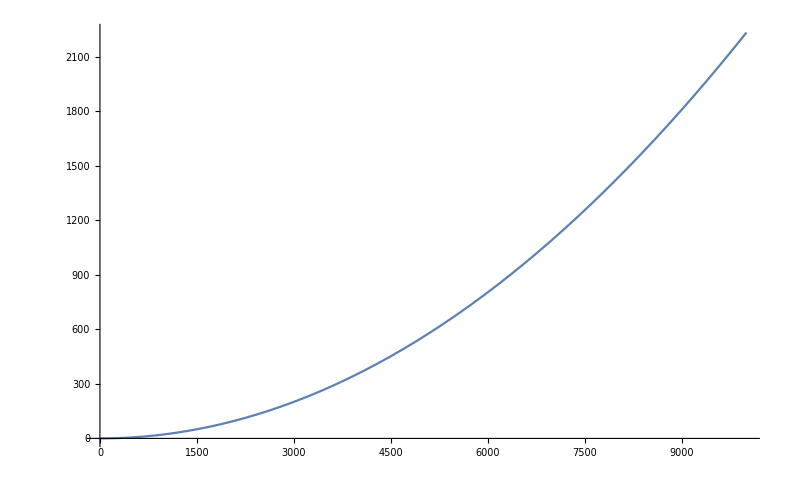

```mathematica
Plot[thrust[rotation]/9.81,{rotation,0,10000}]
```

```mathematica
sqrdRot[0,0.15,0,0,0,0]
```

sqrdRot[0,0.15,0,0,0,0]

```mathematica
sqrdRot[0,0,-2.5 9.80665,0,0,0]
```

sqrdRot[0,0,-24.5166,0,0,0]

```mathematica
sqrdRot[0,0,-2.5 9.80665,0,0,0]//MatrixForm
sqrdRot[0,0,-2.5 9.80665,0,0,0]^(1/2)//MatrixForm
sgn=Sign[sqrdRot[0,0,-2.5 9.80665,0,0,0]];
```

sqrdRot[0,0,-24.5166,0,0,0]

√sqrdRot[0,0,-24.5166,0,0,0]

```mathematica
25000^1/2
```

12500

```mathematica
sgn=Sign[sqrdRot[0,0.15,-1.91 9.80665,0,0,0]]
```

Sign[sqrdRot[0,0.15,-18.7307,0,0,0]]

```mathematica
5.4/9.80665
```

0.550647

## III.h - Exporting the figure of the prototype model with the normal vectors of the engines

Rever os gráfs dos vetores. É possível que eles estejam gerando conflito.

```mathematica
bodypropellersname1=FileNameJoin[{FileNameJoin[{(*FileNameDrop[*)NotebookDirectory[](*,-1]*),"fig"}],"bodypropellersdirections1.png"}];
```

```mathematica
bodypropellersname2=FileNameJoin[{FileNameJoin[{(*FileNameDrop[*)NotebookDirectory[](*,-1]*),"fig"}],"bodypropellersdirections2.png"}];
```

```mathematica
bodypropellersname3=FileNameJoin[{FileNameJoin[{(*FileNameDrop[*)NotebookDirectory[](*,-1]*),"stl"}],"bodypropellersdirections.stl"}];
```

```mathematica
Export[bodypropellersname1,plotZdirections1]
```

/home/oem/Documents/OneDriver/cursos/puc/00_DISSERTAÇÃO/04_Desenvolvimentos/C_Modelagens/Problemas de Otimização/fig/bodypropellersdirections1.png

```mathematica
(*Export[bodypropellersname2,plotZdirections2]*)
Export[bodypropellersname2,plotZdirections3]
```

Part::partw: Part 2 of Sign[sqrdRot[0,0.15,-18.7307,0,0,0]] does not exist.

Part::partw: Part 3 of Sign[sqrdRot[0,0.15,-18.7307,0,0,0]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

/home/oem/Documents/OneDriver/cursos/puc/00_DISSERTAÇÃO/04_Desenvolvimentos/C_Modelagens/Problemas de Otimização/fig/bodypropellersdirections2.png

```mathematica
Export[bodypropellersname3,plotZdirections3, {"STL", "BinaryFormat" -> False}]
```

Part::partw: Part 2 of Sign[sqrdRot[0,0.15,-18.7307,0,0,0]] does not exist.

Part::partw: Part 3 of Sign[sqrdRot[0,0.15,-18.7307,0,0,0]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

/home/oem/Documents/OneDriver/cursos/puc/00_DISSERTAÇÃO/04_Desenvolvimentos/C_Modelagens/Problemas de Otimização/stl/bodypropellersdirections.stl

```mathematica
Export[bodypropellersname3,plotZdirections3]
```

Part::partw: Part 2 of Sign[sqrdRot[0,0.15,-18.7307,0,0,0]] does not exist.

Part::partw: Part 3 of Sign[sqrdRot[0,0.15,-18.7307,0,0,0]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

/home/oem/Documents/OneDriver/cursos/puc/00_DISSERTAÇÃO/04_Desenvolvimentos/C_Modelagens/Problemas de Otimização/stl/bodypropellersdirections.stl

```mathematica
Import[%]
```

$Aborted

```mathematica
Export[bodypropellersname2,plotZdirections2]
```

C:\Users\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Problemas de Otimização\stl\bodypropellersdirections.stl

Cálculos Y

```mathematica
YY=mappingY;
```

```mathematica
{unit,sing,value}=.;
{umatrix,singmatrix,vmatrix}=SingularValueDecomposition[YY];
Dimensions[umatrix];
Dimensions[singmatrix];
Dimensions[vmatrix];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ((-1/2-1/(2 √3))/(√3)+(1/2-1/(2 √3))/(√3))/(√3)-((-1/2-1/(2 √3))/(√3)+(1/2-1/(2 √3))/(√3)) ((1/2-1/(2 √3))/(√3)+(1/2+1/(2 √3))/(√3)).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(-1/3+(-1/2-1/(2 √3))/(√3))/(√3)+(-1/3-(1/2+1/(2 √3))/(√3))/(√3).

General::stop: Further output of N::meprec will be suppressed during this calculation.

```mathematica
umatrix//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
umatrix.Transpose[umatrix]//MatrixForm
Transpose[umatrix].umatrix//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Dimensions[umatrix]
```

{6,6}

```mathematica
Dimensions[singmatrix]
```

{6,8}

```mathematica
θθ=2;
N[vmatrix,θθ].Transpose[N[vmatrix,θθ]]//MatrixForm
Transpose[N[vmatrix,θθ]].N[vmatrix,θθ]//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0
0. | 0. | 0. | 0. | 0. | 0. | 0 | 1.)

```mathematica
N[singmatrix,3].Transpose[N[singmatrix,3]]//MatrixForm
Transpose[N[singmatrix,3]].N[singmatrix,3]//MatrixForm
```

(2.7 | 0 | 0 | 0 | 0 | 0
0 | 2.7 | 0 | 0 | 0 | 0
0 | 0 | 2.7 | 0 | 0 | 0
0 | 0 | 0 | 2.7 | 0 | 0
0 | 0 | 0 | 0 | 2.7 | 0
0 | 0 | 0 | 0 | 0 | 2.7)

(2.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2.7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2.7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2.7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
vmatrix
```

```mathematica
Factor
```

```mathematica
singmatrix//MatrixForm
```

(2 √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 √(2/3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 √(2/3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 √(2/3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 √(2/3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 √(2/3) | 0 | 0)

```mathematica
PseudoInverse[singmatrix]//MatrixForm//N
```

(0.612372 | 0. | 0. | 0. | 0. | 0.
0. | 0.612372 | 0. | 0. | 0. | 0.
0. | 0. | 0.612372 | 0. | 0. | 0.
0. | 0. | 0. | 0.612372 | 0. | 0.
0. | 0. | 0. | 0. | 0.612372 | 0.
0. | 0. | 0. | 0. | 0. | 0.612372
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
MatrixForm[vmatrix]//N
```

(0.353553 | -0.482963 | 0.12941 | 0.353553 | 0.12941 | -0.482963 | 0. | 0.5
-0.353553 | -0.12941 | -0.482963 | -0.353553 | 0.482963 | 0.12941 | 0. | 0.5
-0.353553 | 0.12941 | 0.482963 | -0.353553 | -0.482963 | -0.12941 | 0. | 0.5
0.353553 | 0.482963 | -0.12941 | 0.353553 | -0.12941 | 0.482963 | 0. | 0.5
-0.353553 | -0.482963 | 0.12941 | 0.353553 | -0.12941 | 0.482963 | 0.5 | 0.
0.353553 | -0.12941 | -0.482963 | -0.353553 | -0.482963 | -0.12941 | 0.5 | 0.
0.353553 | 0.12941 | 0.482963 | -0.353553 | 0.482963 | 0.12941 | 0.5 | 0.
-0.353553 | 0.482963 | -0.12941 | 0.353553 | 0.12941 | -0.482963 | 0.5 | 0.)

```mathematica
Inverse[Transpose[vmatrix]]//MatrixForm//N
```

(0.353553 | -0.482963 | 0.12941 | 0.353553 | 0.12941 | -0.482963 | -6.93889×10^-18 | 0.5
-0.353553 | -0.12941 | -0.482963 | -0.353553 | 0.482963 | 0.12941 | 8.67362×10^-19 | 0.5
-0.353553 | 0.12941 | 0.482963 | -0.353553 | -0.482963 | -0.12941 | 8.67362×10^-19 | 0.5
0.353553 | 0.482963 | -0.12941 | 0.353553 | -0.12941 | 0.482963 | -6.93889×10^-18 | 0.5
-0.353553 | -0.482963 | 0.12941 | 0.353553 | -0.12941 | 0.482963 | 0.5 | -6.93889×10^-18
0.353553 | -0.12941 | -0.482963 | -0.353553 | -0.482963 | -0.12941 | 0.5 | 8.67362×10^-19
0.353553 | 0.12941 | 0.482963 | -0.353553 | 0.482963 | 0.12941 | 0.5 | -8.67362×10^-19
-0.353553 | 0.482963 | -0.12941 | 0.353553 | 0.12941 | -0.482963 | 0.5 | 6.93889×10^-18)

```mathematica
Inverse[umatrix].umatrix//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
PseudoInverse[singmatrix]//MatrixForm
```

((√(3/2))/2 | 0 | 0 | 0 | 0 | 0
0 | (√(3/2))/2 | 0 | 0 | 0 | 0
0 | 0 | (√(3/2))/2 | 0 | 0 | 0
0 | 0 | 0 | (√(3/2))/2 | 0 | 0
0 | 0 | 0 | 0 | (√(3/2))/2 | 0
0 | 0 | 0 | 0 | 0 | (√(3/2))/2
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
PseudoInverse[singmatrix].singmatrix//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Inverse[umatrix].PseudoInverse[singmatrix].Inverse[Transpose[vmatrix]]//MatrixForm//N
```

{{0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.}}.{{0.612372,0.,0.,0.,0.,0.},{0.,0.612372,0.,0.,0.,0.},{0.,0.,0.612372,0.,0.,0.},{0.,0.,0.,0.612372,0.,0.},{0.,0.,0.,0.,0.612372,0.},{0.,0.,0.,0.,0.,0.612372},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}.{{0.353553,-0.482963,0.12941,0.353553,0.12941,-0.482963,-6.93889×10^-18,0.5},{-0.353553,-0.12941,-0.482963,-0.353553,0.482963,0.12941,8.67362×10^-19,0.5},{-0.353553,0.12941,0.482963,-0.353553,-0.482963,-0.12941,8.67362×10^-19,0.5},{0.353553,0.482963,-0.12941,0.353553,-0.12941,0.482963,-6.93889×10^-18,0.5},{-0.353553,-0.482963,0.12941,0.353553,-0.12941,0.482963,0.5,-6.93889×10^-18},{0.353553,-0.12941,-0.482963,-0.353553,-0.482963,-0.12941,0.5,8.67362×10^-19},{0.353553,0.12941,0.482963,-0.353553,0.482963,0.12941,0.5,-8.67362×10^-19},{-0.353553,0.482963,-0.12941,0.353553,0.12941,-0.482963,0.5,6.93889×10^-18}}

```mathematica
(YY.Transpose[YY])//MatrixForm//N
(YY.Transpose[YY])^(.5)//MatrixForm//N
singmatrix//MatrixForm//N
```

(2.66667 | 0. | 0. | 0. | 0. | 0.
0. | 2.66667 | 0. | 0. | 0. | 0.
0. | 0. | 2.66667 | 0. | 0. | 0.
0. | 0. | 0. | 2.66667 | 0. | 0.
0. | 0. | 0. | 0. | 2.66667 | 0.
0. | 0. | 0. | 0. | 0. | 2.66667)

(1.63299 | 0. | 0. | 0. | 0. | 0.
0. | 1.63299 | 0. | 0. | 0. | 0.
0. | 0. | 1.63299 | 0. | 0. | 0.
0. | 0. | 0. | 1.63299 | 0. | 0.
0. | 0. | 0. | 0. | 1.63299 | 0.
0. | 0. | 0. | 0. | 0. | 1.63299)

(1.63299 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.63299 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.63299 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.63299 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.63299 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.63299 | 0. | 0.)

```mathematica
(YY.Transpose[YY].YY)//MatrixForm//N
```

(-2.10313 | 0.563533 | -0.563533 | 2.10313 | 2.10313 | -0.563533 | 0.563533 | -2.10313
0.563533 | 2.10313 | -2.10313 | -0.563533 | -0.563533 | -2.10313 | 2.10313 | 0.563533
1.5396 | -1.5396 | -1.5396 | 1.5396 | 1.5396 | -1.5396 | -1.5396 | 1.5396
0.563533 | -2.10313 | 2.10313 | -0.563533 | 0.563533 | -2.10313 | 2.10313 | -0.563533
-2.10313 | -0.563533 | 0.563533 | 2.10313 | -2.10313 | -0.563533 | 0.563533 | 2.10313
1.5396 | -1.5396 | -1.5396 | 1.5396 | -1.5396 | 1.5396 | 1.5396 | -1.5396)

```mathematica
(PseudoInverse[YY].YY.PseudoInverse[YY])//MatrixForm//N
Transpose[YY].Transpose[PseudoInverse[YY]].PseudoInverse[YY]//MatrixForm//N
Transpose[(YY.PseudoInverse[YY])]//MatrixForm//N
```

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 2.77556×10^-17
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 2.77556×10^-17 | 0. | 1.)

```mathematica
PseudoInverse[(YY.PseudoInverse[YY])].(YY.PseudoInverse[YY])//MatrixForm//N
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 5.55112×10^-17
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 5.55112×10^-17 | 0. | 1.)

```mathematica
PseudoInverse[YY].YY.Transpose[YY]//MatrixForm//N
```

(-0.788675 | 0.211325 | 0.57735 | 0.211325 | -0.788675 | 0.57735
0.211325 | 0.788675 | -0.57735 | -0.788675 | -0.211325 | -0.57735
-0.211325 | -0.788675 | -0.57735 | 0.788675 | 0.211325 | -0.57735
0.788675 | -0.211325 | 0.57735 | -0.211325 | 0.788675 | 0.57735
0.788675 | -0.211325 | 0.57735 | 0.211325 | -0.788675 | -0.57735
-0.211325 | -0.788675 | -0.57735 | -0.788675 | -0.211325 | 0.57735
0.211325 | 0.788675 | -0.57735 | 0.788675 | 0.211325 | 0.57735
-0.788675 | 0.211325 | 0.57735 | -0.211325 | 0.788675 | -0.57735)

```mathematica
MatrixRank[mappingY]
```

6

```mathematica
YY.Transpose[YY]//MatrixForm//N
```

(2.66667 | 0. | 0. | 0. | 0. | 0.
0. | 2.66667 | 0. | 0. | 0. | 0.
0. | 0. | 2.66667 | 0. | 0. | 0.
0. | 0. | 0. | 2.66667 | 0. | 0.
0. | 0. | 0. | 0. | 2.66667 | 0.
0. | 0. | 0. | 0. | 0. | 2.66667)

{Y}.{Y+} = {I}

```mathematica
mappingY//MatrixForm//N
PseudoInverse[mappingY]//MatrixForm//N
```

(-0.788675 | 0.211325 | -0.211325 | 0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675
0.211325 | 0.788675 | -0.788675 | -0.211325 | -0.211325 | -0.788675 | 0.788675 | 0.211325
0.57735 | -0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735 | 0.57735
0.211325 | -0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675 | 0.788675 | -0.211325
-0.788675 | -0.211325 | 0.211325 | 0.788675 | -0.788675 | -0.211325 | 0.211325 | 0.788675
0.57735 | -0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735)

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

```mathematica
mappingY.PseudoInverse[mappingY].mappingY//MatrixForm//N
PseudoInverse[mappingY].mappingY.PseudoInverse[mappingY]//MatrixForm//N
```

(-0.788675 | 0.211325 | -0.211325 | 0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675
0.211325 | 0.788675 | -0.788675 | -0.211325 | -0.211325 | -0.788675 | 0.788675 | 0.211325
0.57735 | -0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735 | 0.57735
0.211325 | -0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675 | 0.788675 | -0.211325
-0.788675 | -0.211325 | 0.211325 | 0.788675 | -0.788675 | -0.211325 | 0.211325 | 0.788675
0.57735 | -0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735)

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

```mathematica
mappingY.PseudoInverse[mappingY]//MatrixForm//N
Transpose[mappingY].Inverse[mappingY.Transpose[mappingY]]//MatrixForm//N
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 2.77556×10^-17
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 2.77556×10^-17 | 0. | 1.)

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

```mathematica
Dimensions[matrixP]
Dimensions[matrixX]
```

{3,8}

{3,8}

```mathematica
Transpose[matrixXX]
```

Transpose[matrixXX]

```mathematica
Transpose[matrixXX][[1]]
Transpose[matrixPP][[1]]
```

matrixXX

matrixPP

```mathematica
matrixPP = {{alpha1,beta1,charlie1,delta1},{alpha2,beta2,charlie2,delta2},{alpha3,beta3,charlie3,delta3}};
matrixXX = {{alpha4,beta4,charlie4,delta4},{alpha5,beta5,charlie5,delta5},{alpha6,beta6,charlie6,delta6}};
matrixPPXX = Transpose[Table[tilmatrix[Evaluate[Transpose[matrixPP][[i]]]].Transpose[matrixXX][[i]] ,{i,1,Dimensions[matrixPP][[2]]}]];(*Cross between the P(i) and X(i) column vector*)
Dimensions[matrixPPXX]
matrixPPXX//MatrixForm
```

{3,4}

(-alpha3 alpha5+alpha2 alpha6 | -beta3 beta5+beta2 beta6 | -charlie3 charlie5+charlie2 charlie6 | -delta3 delta5+delta2 delta6
alpha3 alpha4-alpha1 alpha6 | beta3 beta4-beta1 beta6 | charlie3 charlie4-charlie1 charlie6 | delta3 delta4-delta1 delta6
-alpha2 alpha4+alpha1 alpha5 | -beta2 beta4+beta1 beta5 | -charlie2 charlie4+charlie1 charlie5 | -delta2 delta4+delta1 delta5)

```mathematica
testmatrix=PseudoInverse[mappingY].mappingY;testmatrix//MatrixForm//FullSimplify
```

(3/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 0 | 0
-1/4 | 3/4 | -1/4 | -1/4 | 0 | 0 | 0 | 0
-1/4 | -1/4 | 3/4 | -1/4 | 0 | 0 | 0 | 0
-1/4 | -1/4 | -1/4 | 3/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3/4 | -1/4 | -1/4 | -1/4
0 | 0 | 0 | 0 | -1/4 | 3/4 | -1/4 | -1/4
0 | 0 | 0 | 0 | -1/4 | -1/4 | 3/4 | -1/4
0 | 0 | 0 | 0 | -1/4 | -1/4 | -1/4 | 3/4)

```mathematica
Det[testmatrix]
```

0

```mathematica
Det[Transpose[mappingY].mappingY]
```

0

Because Rank of {Y}mn matrix is “n”, with m > n, A^+ = n x n

SingularValueDecomposition[]

```mathematica
{unit,sing,value}=SingularValueDecomposition[N[mappingY]];
```

```mathematica
(*Verificar se a parcela P x X pode ser normalizado*)
```

```mathematica
Transpose[unit].unit//MatrixForm//N
Transpose[value].value//MatrixForm//N
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 1.11022×10^-16 | 5.55112×10^-17
0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 1.11022×10^-16 | 0. | 1. | -5.55112×10^-17
0. | 0. | 5.55112×10^-17 | 0. | -5.55112×10^-17 | 1.)

(1. | 2.08167×10^-17 | -7.11237×10^-17 | 5.55112×10^-17 | 2.77556×10^-17 | -2.77556×10^-17 | 0. | -2.77556×10^-17
2.08167×10^-17 | 1. | 4.68375×10^-17 | 2.77556×10^-17 | -6.93889×10^-17 | -4.51028×10^-17 | 3.46945×10^-18 | 2.77556×10^-17
-7.11237×10^-17 | 4.68375×10^-17 | 1. | -3.98986×10^-17 | 0. | 6.89553×10^-17 | -9.45424×10^-17 | -6.07153×10^-17
5.55112×10^-17 | 2.77556×10^-17 | -3.98986×10^-17 | 1. | 0. | -4.85723×10^-17 | 2.77556×10^-17 | -5.55112×10^-17
2.77556×10^-17 | -6.93889×10^-17 | 0. | 0. | 1. | -8.32667×10^-17 | 1.80411×10^-16 | 1.11022×10^-16
-2.77556×10^-17 | -4.51028×10^-17 | 6.89553×10^-17 | -4.85723×10^-17 | -8.32667×10^-17 | 1. | -1.59595×10^-16 | 1.31839×10^-16
0. | 3.46945×10^-18 | -9.45424×10^-17 | 2.77556×10^-17 | 1.80411×10^-16 | -1.59595×10^-16 | 1. | 1.38778×10^-17
-2.77556×10^-17 | 2.77556×10^-17 | -6.07153×10^-17 | -5.55112×10^-17 | 1.11022×10^-16 | 1.31839×10^-16 | 1.38778×10^-17 | 1.)

```mathematica
unit//MatrixForm
sing//MatrixForm
value//MatrixForm
```

(0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | -0.248069 | 0. | 0.372104 | 0.894427
1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | -0.496139 | 0. | 0.744208 | -0.447214
0. | 0. | -0.83205 | 0. | -0.5547 | 0.)

(1.63299 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.63299 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.63299 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.63299 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.63299 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.63299 | 0. | 0.)

(0.353553 | 0.12941 | -0.08666 | -0.482963 | -0.507387 | 0.331735 | 0.463189 | -0.188298
-0.353553 | -0.482963 | 0.238571 | 0.12941 | 0.279521 | 0.489849 | 0.463189 | -0.188298
-0.353553 | 0.482963 | 0.349777 | -0.12941 | 0.112711 | -0.489849 | 0.463189 | -0.188298
0.353553 | -0.12941 | -0.501688 | 0.482963 | 0.115155 | -0.331735 | 0.463189 | -0.188298
0.353553 | 0.12941 | 0.565893 | 0.482963 | -0.211463 | 0.10024 | 0.188298 | 0.463189
-0.353553 | -0.482963 | -0.110161 | -0.12941 | -0.472136 | -0.374101 | 0.188298 | 0.463189
-0.353553 | 0.482963 | -0.478188 | 0.12941 | 0.079904 | 0.374101 | 0.188298 | 0.463189
0.353553 | -0.12941 | 0.0224549 | -0.482963 | 0.603695 | -0.10024 | 0.188298 | 0.463189)

```mathematica
Inverse[unit].unit//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 2.77556×10^-17
0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 5.55112×10^-17
0. | 0. | 1.9346×10^-17 | 0. | -5.60641×10^-18 | 1.)

```mathematica
teste=PseudoInverse[mappingY].mappingY;
```

```mathematica
teste//N//MatrixForm
Det[teste]
```

(0.75 | -0.25 | -0.25 | -0.25 | -1.38778×10^-17 | 2.77556×10^-17 | 2.77556×10^-17 | 0.
-0.25 | 0.75 | -0.25 | -0.25 | 2.77556×10^-17 | -1.38778×10^-17 | 0. | 2.77556×10^-17
-0.25 | -0.25 | 0.75 | -0.25 | 2.77556×10^-17 | 0. | -1.38778×10^-17 | 2.77556×10^-17
-0.25 | -0.25 | -0.25 | 0.75 | 0. | 2.77556×10^-17 | 2.77556×10^-17 | -1.38778×10^-17
-1.38778×10^-17 | 2.77556×10^-17 | 2.77556×10^-17 | 0. | 0.75 | -0.25 | -0.25 | -0.25
2.77556×10^-17 | -1.38778×10^-17 | 0. | 2.77556×10^-17 | -0.25 | 0.75 | -0.25 | -0.25
2.77556×10^-17 | 0. | -1.38778×10^-17 | 2.77556×10^-17 | -0.25 | -0.25 | 0.75 | -0.25
0. | 2.77556×10^-17 | 2.77556×10^-17 | -1.38778×10^-17 | -0.25 | -0.25 | -0.25 | 0.75)

0

```mathematica
2^100
N[2^100]
```

1267650600228229401496703205376

1.26765×10^30

```mathematica
N[2^100,10]
```

1.2676506×10^30

```mathematica
piY.mappingY
```

```mathematica
piY.mappingY//N//MatrixForm
```

(0.75 | -0.25 | -0.25 | -0.25 | -2.77556×10^-17 | 2.77556×10^-17 | 4.16334×10^-17 | -2.77556×10^-17
-0.25 | 0.75 | -0.25 | -0.25 | 2.77556×10^-17 | 0. | -4.16334×10^-17 | 2.77556×10^-17
-0.25 | -0.25 | 0.75 | -0.25 | 2.77556×10^-17 | -4.16334×10^-17 | 0. | 2.77556×10^-17
-0.25 | -0.25 | -0.25 | 0.75 | -2.77556×10^-17 | 4.16334×10^-17 | 2.77556×10^-17 | -2.77556×10^-17
-2.77556×10^-17 | 2.77556×10^-17 | 4.16334×10^-17 | -2.77556×10^-17 | 0.75 | -0.25 | -0.25 | -0.25
2.77556×10^-17 | 0. | -4.16334×10^-17 | 2.77556×10^-17 | -0.25 | 0.75 | -0.25 | -0.25
2.77556×10^-17 | -4.16334×10^-17 | 0. | 2.77556×10^-17 | -0.25 | -0.25 | 0.75 | -0.25
-2.77556×10^-17 | 4.16334×10^-17 | 2.77556×10^-17 | -2.77556×10^-17 | -0.25 | -0.25 | -0.25 | 0.75)

```mathematica
Norm[mappingY]//N
```

1.63299

```mathematica
mappingY//MatrixForm//N
piY//MatrixForm//N
```

(-0.788675 | 0.211325 | -0.211325 | 0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675
0.211325 | 0.788675 | -0.788675 | -0.211325 | -0.211325 | -0.788675 | 0.788675 | 0.211325
0.57735 | -0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735 | -0.57735 | 0.57735
0.211325 | -0.788675 | 0.788675 | -0.211325 | 0.211325 | -0.788675 | 0.788675 | -0.211325
-0.788675 | -0.211325 | 0.211325 | 0.788675 | -0.788675 | -0.211325 | 0.211325 | 0.788675
0.57735 | -0.57735 | -0.57735 | 0.57735 | -0.57735 | 0.57735 | 0.57735 | -0.57735)

(-0.295753 | 0.0792468 | 0.216506 | 0.0792468 | -0.295753 | 0.216506
0.0792468 | 0.295753 | -0.216506 | -0.295753 | -0.0792468 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | 0.295753 | 0.0792468 | -0.216506
0.295753 | -0.0792468 | 0.216506 | -0.0792468 | 0.295753 | 0.216506
0.295753 | -0.0792468 | 0.216506 | 0.0792468 | -0.295753 | -0.216506
-0.0792468 | -0.295753 | -0.216506 | -0.295753 | -0.0792468 | 0.216506
0.0792468 | 0.295753 | -0.216506 | 0.295753 | 0.0792468 | 0.216506
-0.295753 | 0.0792468 | 0.216506 | -0.0792468 | 0.295753 | -0.216506)

```mathematica
NSqrd[0,0,(1.91 9.80665) 1.1,0,0,0,1.91]//MatrixForm
(NSqrd[0,0,(1.91 9.80665) 1.1,0,0,0,1.91]/sgn[0,0,(1.91 9.80665) 1.1,0,0,0,1.91])^(1/2)//MatrixForm

rotationN=((NSqrd[0,0,(1.91 9.80665) 1.1,0,0,0,1.91]/sgn)^(1/2))*60/2 Pi
rotationN2=rotationN sgn;rotationN2//MatrixForm
```

(9364.93
-9364.93
-9364.93
9364.93
9364.93
-9364.93
-9364.93
9364.93)

(96.7726
96.7726
96.7726
96.7726
96.7726
96.7726
96.7726
96.7726)

{9120.6,9120.6,9120.6,9120.6,9120.6,9120.6,9120.6,9120.6}

(9120.6
-9120.6
-9120.6
9120.6
9120.6
-9120.6
-9120.6
9120.6)

```mathematica
((1.91 9.80665) 1.1)-(1.91 9.80665)
```

1.87307